```mathematica
{0,1}
```

{0,1}

```mathematica
{(1-p)#,#+p(1-#)}&/@%
```

{{0,p},{1-p,1}}

```mathematica
Flatten@%
```

{0,p,1-p,1}

```mathematica
{(1-q)#,#+q(1-#)}&/@%
```

{{0,q},{p (1-q),p+(1-p) q},{(1-p) (1-q),1-p+p q},{1-q,1}}

```mathematica
Flatten@%
```

{0,q,p (1-q),p+(1-p) q,(1-p) (1-q),1-p+p q,1-q,1}

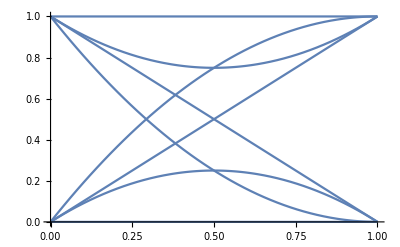

```mathematica
Plot[%5/.{p->q},{q,0,1}]
```

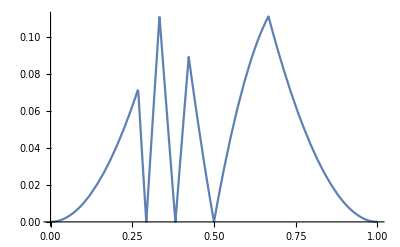

```mathematica
Plot[f[p],{p,0,1}]
f[v_]:=Min[Differences[Sort[%5/.{q->v,p->v}]]]
```

```mathematica
m[x_,y_]:=Min[Differences[Sort[%5/.{q->y,p->x}]]];
MaximalBy[Join@@Table[{x,y,m[x,y]},{x,2/3,2/3},{y,0,1,.0001}],#[[3]]&]
```

{{2/3,0.5715,0.142833}}

```mathematica
f[.27]
```

0.0658

```mathematica
f[.7]
```

0.09

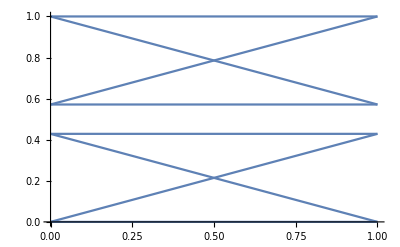

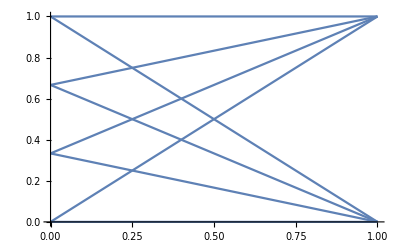

```mathematica
Plot[%5/.{q->(4/7)},{p,0,1}]
Plot[%5/.{p->(1/3)},{q,0,1}]
```

```mathematica
%5/.{q->(4/7),p->(1/3)}
%5/.{q->(1/7),p->(1/3)}
%5/.{q->(4/7),p->(2/3)}
```

{0,4/7,1/7,5/7,2/7,6/7,3/7,1}

{0,1/7,2/7,3/7,4/7,5/7,6/7,1}

{0,4/7,2/7,6/7,1/7,5/7,3/7,1}

```mathematica
{4/7,2/7,1/7}
```